## Model of a pathogen making β-lactamase

#### This document includes:

In-patch model, analysis, and figures used for Supplemental discussion 3: “A model of β-lactamase production exhibits a competition-colonization trade-off”

Code to generate Figure 6B, 6C

## Model

```mathematica
ODEs = {
Bug'==((1-α)* γ*Food-d-Toxin)*Bug,
Food'==foodIn-d*Food-Bug*Food,
Toxin' ==ToxinIn-d*Toxin-Bug*Toxin-Antitoxin*Toxin,
Antitoxin'==α*ϵ*Bug-Antitoxin*d
};
params={
d->0.1,
foodIn->1,
ToxinIn->0.9,
γ -> 1,
ϵ -> 1
};
```

### Extinction equilibrium

```mathematica
Solve[Map[0==#[[2]]&,ODEs]/.{Bug->0}, {Food, Toxin, Antitoxin}]
```

{{Food→foodIn/d,Toxin→ToxinIn/d,Antitoxin→0}}

#### Jacobian

```mathematica
rhs =Map[Last,ODEs]
jac=Map[D[rhs, #]&, {Bug, Food, Toxin, Antitoxin}];
Simplify[jac]//MatrixForm
```

{Bug (-d-Toxin+Food (1-α) γ),-Bug Food-d Food+foodIn,-Antitoxin Toxin-Bug Toxin-d Toxin+ToxinIn,-Antitoxin d+Bug α ϵ}

(-d-Toxin-Food (-1+α) γ | -Food | -Toxin | α ϵ
-Bug (-1+α) γ | -Bug-d | 0 | 0
-Bug | 0 | -Antitoxin-Bug-d | 0
0 | 0 | -Toxin | -d)

```mathematica
Eigenvalues[jac/.{Bug->0, Food->foodIn/d, Toxin->ToxinIn/d,Antitoxin->0}]
```

{-d,-d,-d,(-d^2-ToxinIn+foodIn γ-foodIn α γ)/d}

Eigenvalues become negative (extinction is stable) when

```mathematica
Solve[(-d^2+foodIn-ToxinIn-foodIn α)/d==0,α]
```

{{α→(-d^2+foodIn-ToxinIn)/foodIn}}

```mathematica
%/.params
```

{{α→0.09}}

So there is not necessarily a strong Allee effect.

#### Stable positive equilibrium:

```mathematica
sol=Solve[Map[0==#[[2]]&,ODEs], {Bug,Food,Toxin,Antitoxin}];
```

```mathematica
sol/.params/.{α->0.2}
```

{{Bug→0,Food→10.,Toxin→9.,Antitoxin→0},{Bug→4.85912,Food→0.201649,Toxin→0.0613189,Antitoxin→9.71824},{Bug→0.00754595,Food→9.29835,Toxin→7.33868,Antitoxin→0.0150919}}

Solution 2 is positive and stable. Exact solution for Rust simulation:

```mathematica
FullSimplify[sol[[2]][[1]]]
```

Bug→-1/(2 d (d+α ϵ))(2 d^3+d (ToxinIn+foodIn (-1+α) γ)+d^2 α ϵ+foodIn (-1+α) α γ ϵ-√(4 d^2 foodIn (-1+α) α γ ϵ (d+α ϵ)+(d (ToxinIn+foodIn (-1+α) γ)-d^2 α ϵ+foodIn (-1+α) α γ ϵ)^2))

### NonNegativeReal solutions

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

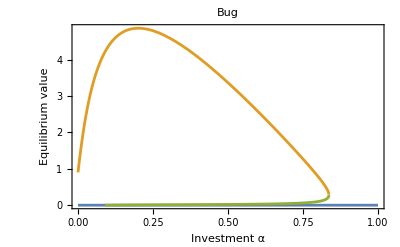
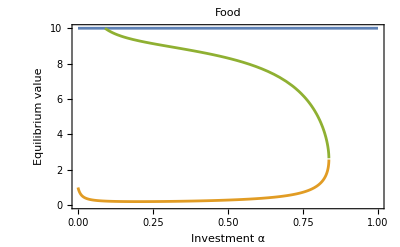
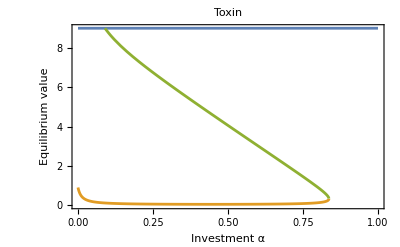
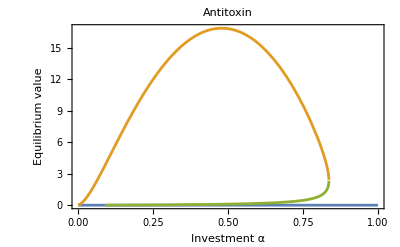

```mathematica
sol=Solve[Map[0==#[[2]]&,ODEs]/.params, {Bug,Food,Toxin,Antitoxin},NonNegativeReals];
Table[Plot[Evaluate[var/.sol/.{α->a}/.params],{a,0, 1},PlotLabel->ToString[var],
Frame->True,FrameLabel->{"Investment α","Equilibrium value"}],{var,{Bug,Food,Toxin,Antitoxin}}]
```

```mathematica
sol/.α->0.00001
```

{{Bug→0,Food→10.,Toxin→9.,Antitoxin→0},{Bug→0.90071,Food→0.999291,Toxin→0.899281,Antitoxin→0.000090071},{Bug→Undefined,Food→Undefined,Toxin→Undefined,Antitoxin→Undefined}}

#### Maximizing biomass

```mathematica
Maximize[{sol[[2]][[1]][[2]][[1]], 0.08<α<0.8},α,PositiveReals]
```

{4.85915,{α→0.201013}}

#### Bifurcation point

```mathematica
bifurcation=sol[[3]][[1]][[2]][[2]][[1]]
```

0.09

### Bifurcation plot (Figure 6B)

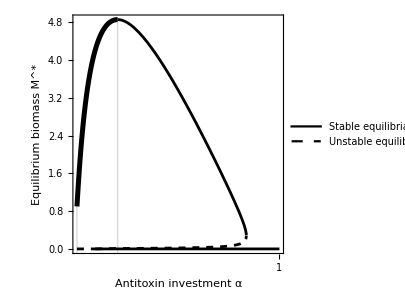

```mathematica
lines=Evaluate[Bug/.sol];
stable=lines[[2]];
lines[[2]]=ConditionalExpression[stable,α>0.201013];
AppendTo[lines, ConditionalExpression[stable,α<0.201013]];
zero=lines[[1]];
lines[[1]]=ConditionalExpression[zero,α>0.09];
AppendTo[lines, ConditionalExpression[zero,α<0.09]];
pltvsalpha=Plot[lines,{α,0,1},
PlotStyle->{Black,Black, {Black,Dashed},{Black,Thickness[0.012]},{Black,Dashed}},
Frame->True,FrameLabel->{"Antitoxin investment α","Equilibrium biomass M^*"},
PlotTheme->"Default",BaseStyle->Directive[FontSize->13,FontColor->Black],LabelStyle->Directive[FontSize->11,FontColor->Black],
PlotLegends->Placed[LineLegend[{Black,{Black,Dashed}},{"Stable equilibria", "Unstable equilibrium"},LegendMarkerSize->{22,10}],{Right,Top}],
PlotRangeClipping->False,
Prolog->{
Directive[LightGray],
Line[{{0,-0.35},{0,0.9}}],
Line[{{0.201013,-0.35},{0.201013,4.859154996561221}}],
Black,FontSize->11,
Text["α_min = 0",{-0.02,-0.44}],
Text["α̂",{0.201013,-0.44}]
},
FrameTicks->{{Automatic,None},{{1},None}},
ImageSize->300,AspectRatio->1
]
```

### CC trade-off (Figure 6C)

```mathematica
Mstar[a_]:=If[a==0,
Bug/.Solve[Map[0==#[[2]]&,ODEs]/.params/.α->0, {Bug,Food,Toxin,Antitoxin},NonNegativeReals][[2]],
Bug/.sol[[2]]/.α->a
]
Rstar[a_]:=1/(1-α) /.α->a
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

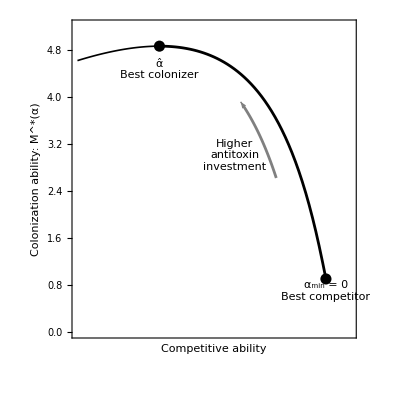

```mathematica
Show[ParametricPlot[Evaluate@{1/Rstar[a],Mstar[a]},{a,0,0.201013}, (* frontier *)
PlotStyle->Black,
PlotRange->{{0.7,1.03},{0,5.2}},
Frame->True,FrameLabel->{"Competitive ability","Colonization ability: M^*(α)"},
FrameTicks->{{Automatic,None},{None,None}},
PlotTheme->"Default",BaseStyle->Directive[FontSize->13,FontColor->Black],
LabelStyle->Directive[FontSize->13,FontColor->Black],AspectRatio->1,
Epilog->{
Directive[PointSize[0.02]],
Point[{1/Rstar[a],Mstar[a]}/.a->0],
Text["α_min = 0\nBest competitor",{1/Rstar[a],Mstar[a]-0.2}/.a->0,{1,0}],
Point[{1/Rstar[a],Mstar[a]}/.a->0.201013],
Text["α̂\nBest colonizer",{1/Rstar[a],Mstar[a]-0.4}/.a->0.201013],
Directive[Gray],
Arrow[{{1/Rstar[a]-0.03,Mstar[a]}/.(a->0.07), {1/Rstar[a]-0.03,Mstar[a]}/.(a->0.073)}],
Directive[Black,FontSize->11],
Text["Higher\nantitoxin\ninvestment",{0.89,3}]
},
ImageSize->{300}
],
ParametricPlot[Evaluate@{1/Rstar[a],Mstar[a]},{a,0.201013,0.3},PlotStyle->{Black,Thickness[0.003]}],
ParametricPlot[Evaluate@{1/Rstar[a]-0.03,Mstar[a]},{a,0.03,0.07},PlotStyle->Gray] (* arrow*)
]
```

## Zero net growth isoclines (ZNGIs)

```mathematica
tolIridescent = Map[RGBColor,{"#FEFBE9","#FCF7D5","#F5F3C1","#EAF0B5","#DDECBF","#D0E7CA","#C2E3D2","#B5DDD8","#A8D8DC","#9BD2E1","#8DCBE4","#81C4E7","#7BBCE7","#7EB2E4","#88A5DD","#9398D2","#9B8AC4","#9D7DB2","#9A709E","#906388","#805770","#684957","#46353A"}];
colors=tolIridescent[[{7,10,13,16,19,22}]]
```

{RGBColor[0.7607843137254902, 0.8901960784313725, 0.8235294117647058],RGBColor[0.6078431372549019, 0.8235294117647058, 0.8823529411764706],RGBColor[0.4823529411764706, 0.7372549019607844, 0.9058823529411765],RGBColor[0.5764705882352941, 0.596078431372549, 0.8235294117647058],RGBColor[0.6039215686274509, 0.4392156862745098, 0.6196078431372549],RGBColor[0.40784313725490196, 0.28627450980392155, 0.3411764705882353]}

```mathematica
ODEs = {
0==((1-α)*Food-d-Toxin)*Bug,
0==foodIn-d*Food-Bug*Food,
0 ==ToxinIn-d*Toxin-Bug*Toxin-Antitoxin*Toxin,
0==α*Bug-Antitoxin*d
};
params={
d->0.1,
foodIn->1,
ToxinIn->0.9
};
```

```mathematica
zngi =0==(1-α)*Food-d-Toxin;
```

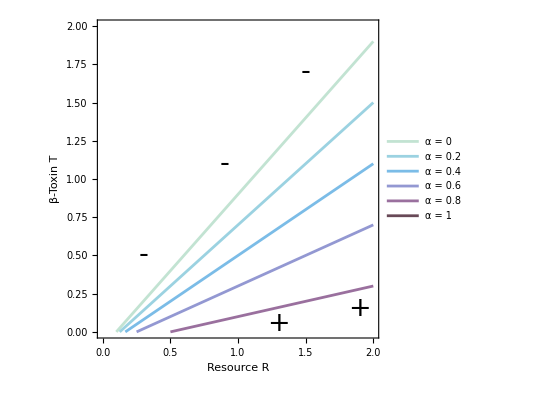

```mathematica
ContourPlot[
Evaluate[Table[
zngi/.params,
{α,{0,0.2,0.4,0.6,0.8,1}}
]]
,{Food,0,2},{Toxin,0,2},
ContourStyle->colors,
PlotLegends->Placed[
Map["α = "<>ToString[#]&,{0,0.2,0.4,0.6,0.8,1}],
{Left, Top}],
BaseStyle->Directive[FontSize->13,FontColor->Black],
LabelStyle->Directive[FontColor->Black],
Epilog->{
Black,Text[Style["-",27],{0.3,0.5}],
Black,Text[Style["-",27],{0.9, 1.1}],
Black,Text[Style["-",27],{1.5,1.7}],
Black,Text[Style["+",27],{1.3,0.05}],
Black,Text[Style["+",27],{1.9,0.15}]
},
Frame->True,FrameLabel->{"Resource R","β-Toxin T"}]
```